```mathematica
ψ[x_,n_,L_]:=√(2/L)Sin[(n π)/L x]
```

```mathematica
delta[x_,y_,n_,L_]:=Sum[ψ[x,m,L]ψ[y,m,L],{m,1,n}]
```

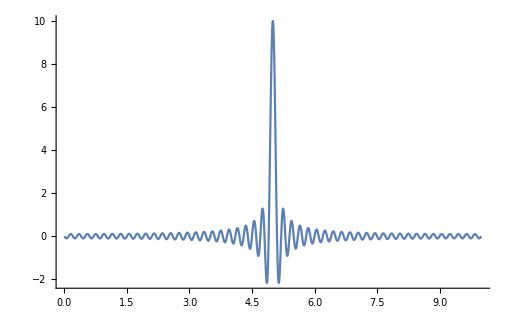

```mathematica
Plot[delta[x,5,100,10],{x,0,10},PlotRange->All]
```

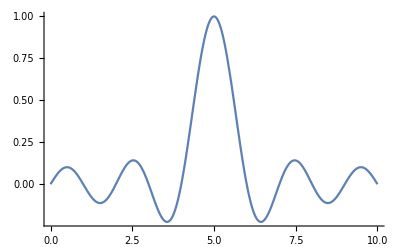

```mathematica
Plot[delta[x,5,10,10],{x,0,10},PlotRange->All]
```

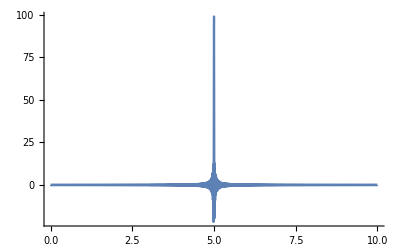

```mathematica
Plot[delta[x,5,1000,10],{x,0,10},PlotRange->All]
```

```mathematica
values = ParallelTable[{n,Integrate[delta[x,50,n,100],{x,0,100}]},{n,1,32}]
```

{{1,4/π},{2,4/π},{3,8/(3 π)},{4,8/(3 π)},{5,52/(15 π)},{6,52/(15 π)},{7,304/(105 π)},{8,304/(105 π)},{9,1052/(315 π)},{10,1052/(315 π)},{11,10312/(3465 π)},{12,10312/(3465 π)},{13,147916/(45045 π)},{14,147916/(45045 π)},{15,135904/(45045 π)},{16,135904/(45045 π)},{17,2490548/(765765 π)},{18,2490548/(765765 π)},{19,44257352/(14549535 π)},{20,44257352/(14549535 π)},{21,47028692/(14549535 π)},{22,47028692/(14549535 π)},{23,1023461776/(334639305 π)},{24,1023461776/(334639305 π)},{25,5385020324/(1673196525 π)},{26,5385020324/(1673196525 π)},{27,15411418072/(5019589575 π)},{28,15411418072/(5019589575 π)},{29,467009482388/(145568097675 π)},{30,467009482388/(145568097675 π)},{31,13895021563328/(4512611027925 π)},{32,13895021563328/(4512611027925 π)}}